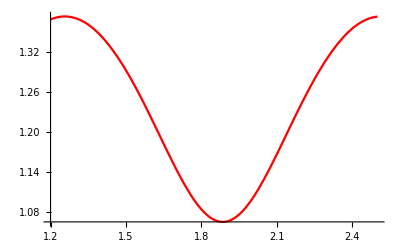

```mathematica
(*Лабораторная работа №5*)
(*гр.221703*)
(*Гаврилович Алиса*)
(*Вариант 3*)

(*Задание №1*)
(*пункт а*)

f[x_]:=(Log[Cos[5*x]+4]^2)^(1/3);
x0=1.82;
gr=Plot[f[x],{x,1.2,2.5},PlotStyle->Red];
Show[gr]
```

```mathematica
(*вычисление производных первого/второго порядка в точке x0 с использованием встроенной функции D*)
```

```mathematica
d11=D[f[x],x]/.x->x0
```

-0.335974

```mathematica
d21=D[f[x],{x,2}]/.x->x0
```

4.76113

```mathematica
(*пункт б*)
```

```mathematica
(*формулы численного дифференцирования*)
deltaY1[y_,y1_]:=y1-y;
deltaY2[y_,y1_,y2_]:=y2-2y1+y;
deltaY3[y_,y1_,y2_,y3_]:=y3-3y2+3y1-y;
h1=0.1;
h2=0.01;
```

```mathematica
pr11=1/h1(deltaY1[f[x0],f[x0+h1]]-1/2*deltaY2[f[x0],f[x0+h1],f[x0+2h1]]+1/3*deltaY3[f[x0],f[x0+h1],f[x0+2h], f[x0+3h1]])
pr12=1/h2(deltaY1[f[x0],f[x0+h2]]-1/2*deltaY2[f[x0],f[x0+h2],f[x0+2h2]]+1/3*deltaY3[f[x0],f[x0+h2],f[x0+2h2], f[x0+3h2]])
```

-0.391676

-0.336037

```mathematica
pr21=1/h1^2(deltaY2[f[x0],f[x0+h1],f[x0+2h1]]-deltaY3[f[x0],f[x0+h1],f[x0+2h1], f[x0+3h1]])
pr22=1/h2^2(deltaY2[f[x0],f[x0+h2],f[x0+2h2]]-deltaY3[f[x0],f[x0+h2],f[x0+2h2], f[x0+3h2]])
```

6.91178

4.78407

```mathematica
(*абсолютные погрешности*)
```

```mathematica
{Abs[d11-pr11],Abs[d21-pr21]}
{Abs[d11-pr12],Abs[d21-pr22]}
```

{0.0557021,2.15065}

{0.0000631254,0.0229394}

```mathematica
(*Вывод: чем меньше шаг,тем меньше абсолютная погрешность результата*)
```

```mathematica
(*Задание 2*)
```

```mathematica
(*пукнт а*)
```

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Tan[1+Csch[1/(x+2)]]^2;
a=-1;
b=3;
h=0.2;
(*формула второго порядка точности*)
data=Table[{x,(f[x+h]-f[x-h])/(2h)},{x,a,b,h}];
TableForm[data]
```

-1. | -864.901
-0.8 | -26.9155
-0.6 | -6.95218
-0.4 | -2.76262
-0.2 | -1.26479
0. | -0.527886
0.2 | -0.0352261
0.4 | 0.434898
0.6 | 1.07608
0.8 | 2.25296
1. | 5.08271
1.2 | 14.8591
1.4 | 91.8864
1.6 | 1266.07
1.8 | -58.5656
2. | -1272.81
2.2 | -35.2457
2.4 | -8.89648
2.6 | -3.51568
2.8 | -1.64916
3. | -0.777568

```mathematica
(*пункт б*)
```

```mathematica
pr1=D[f[x],x]
```

(2 Coth[1/(2+x)] Csch[1/(2+x)] Sec[1+Csch[1/(2+x)]]^2 Tan[1+Csch[1/(2+x)]])/(2+x)^2

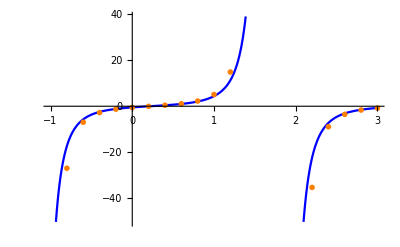

```mathematica
gr=Plot[pr1,{x,a,b},PlotStyle->Blue];
points=ListPlot[data,PlotStyle->{PointSize[0.01],Orange}];
Show[gr,points]
```

```mathematica
(*Задание 3*)
f[x_]:=(2+(3x+1.7)^(1/4))/(x+√(1.5 x^2+1));
a=0.3;
b=0.9;
n1=8;
n2=10;
h1=(b-a)/n1;
h2=(b-a)/n2;
k=2;
```

```mathematica
(*Формула средних прямоугольников*)
```

```mathematica
int1=h1*∑_(i=0)^(n1-1) f[a+i*h1+h1/2]
```

1.11546

```mathematica
int2=h2*∑_(i=0)^(n2-1) f[a+i*h2+h2/2]
```

1.11556

```mathematica
(*Уточнение значения интеграла по Ричардсону*)
```

```mathematica
Richardson=int2+n1^k/(n2^k-n1^k)(int2-int1)
```

1.11574

```mathematica
(*Формула трапеций*)
```

```mathematica
int1=h1*(∑_(i=1)^(n1-1) f[a+i*h1]+f[a]/2+f[a+n1*h1]/2)
```

1.11629

```mathematica
int2=h2*(∑_(i=1)^(n2-1) f[a+i*h2]+f[a]/2+f[a+n2*h2]/2)
```

1.11609

```mathematica
(*Уточнение значения интеграла по Ричардсону*)
```

```mathematica
Richardson=int2+n1^k/(n2^k-n1^k)(int2-int1)
```

1.11574

```mathematica
(*Задание 4*)
(*Разбиение на 8 частей*)
```

```mathematica
data=({{-1, 0.3499}, {-0.95, 0.4055}, {-0.9, 0.3886}, {-0.85, 0.4459}, {-0.8, 0.4317}, {-0.75, 0.4904}, {-0.7, 0.4795}, {-0.65, 0.5392}, {-0.6, 0.5325}, {-0.55, 0.5930}, {-0.5, 0.5915}, {-0.45, 0.6521}, {-0.4, 0.6570}, {-0.35, 0.7171}, {-0.3, 0.7297}, {-0.25, 0.7885}, {-0.2, 0.8105}});
```

```mathematica
a=-1;
b=-0.2;
n=4;
h=(b-a)/(2n);
(*Формула Симпсона*)
int=∑_(i=0)^(n-1) h/3*(data[[2i+1,2]]+4data[[2i+2,2]]+data[[2i+3,2]])
```

0.366867

```mathematica
(*Разбиение на 16 частей*)
n=8;
h=(b-a)/(2n);
int=∑_(i=0)^(n-1) h/3*(data[[2i+1,2]]+4data[[2i+2,2]]+data[[2i+3,2]])
```

0.455137

```mathematica
(*Задание 5*)
```

```mathematica
f[x_]:=Cos[5x+2]/x;
n=7;
a=0.8;
b=2.1;
```

```mathematica
LegendreP[n,t] (*полином Лежандра седьмой степени*)
```

1/16 (-35 t+315 t^3-693 t^5+429 t^7)

```mathematica
sl=NSolve[LegendreP[n,t]==0,t]
```

{{t→-0.949108},{t→-0.741531},{t→-0.405845},{t→0.},{t→0.405845},{t→0.741531},{t→0.949108}}

```mathematica
tt=t/.sl
```

{-0.949108,-0.741531,-0.405845,0.,0.405845,0.741531,0.949108}

```mathematica
T=Table[If[i==1,1,(tt[[j]])^(i-1)],{i,n},{j,n}];MatrixForm[T]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
-0.949108 | -0.741531 | -0.405845 | 0. | 0.405845 | 0.741531 | 0.949108
0.900806 | 0.549868 | 0.16471 | 0. | 0.16471 | 0.549868 | 0.900806
-0.854962 | -0.407745 | -0.0668469 | 0. | 0.0668469 | 0.407745 | 0.854962
0.811451 | 0.302355 | 0.0271295 | 0. | 0.0271295 | 0.302355 | 0.811451
-0.770155 | -0.224206 | -0.0110104 | 0. | 0.0110104 | 0.224206 | 0.770155
0.73096 | 0.166256 | 0.0044685 | 0. | 0.0044685 | 0.166256 | 0.73096)

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N
```

{2.,0.,0.666667,0.,0.4,0.,0.285714}

```mathematica
A=LinearSolve[T,B]  (*Квадратурные коэффициенты Гаусса Subscript[А, i]*)
```

{0.129485,0.279705,0.38183,0.417959,0.38183,0.279705,0.129485}

```mathematica
int=(b-a)/2*∑_(i=1)^n A[[i]]*f[(b+a)/2+(b-a)/2*tt[[i]]]
```

0.0969024

```mathematica
PaddedForm[int, {19,18}]
```

0.096902358500152100

```mathematica
Clear[pr11,pr12,pr21,pr22,f]
```